## BugGuide Data

```mathematica
rawBugGuideData = Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/bugguide.csv"]
```

{{Month,2017,2018,2019,2020},{January,55,50,41,35},{February,195,63,236,99},{March,582,243,443,144},{April,1244,993,742,700},{May,913,664,689,473},{June,153,139,389,103},{July,89,120,294,NA},{August,109,233,294,NA},{September,625,511,393,NA},{October,434,800,624,NA},{November,274,564,216,NA},{December,50,99,65,NA}}

```mathematica
bugGuideData = <|2016+#->Table[{x,rawBugGuideData[[x+1,#+1]]},{x,1,12}]&/@Range[4]|>
```

<|2017→{{1,55},{2,195},{3,582},{4,1244},{5,913},{6,153},{7,89},{8,109},{9,625},{10,434},{11,274},{12,50}},2018→{{1,50},{2,63},{3,243},{4,993},{5,664},{6,139},{7,120},{8,233},{9,511},{10,800},{11,564},{12,99}},2019→{{1,41},{2,236},{3,443},{4,742},{5,689},{6,389},{7,294},{8,294},{9,393},{10,624},{11,216},{12,65}},2020→{{1,35},{2,99},{3,144},{4,700},{5,473},{6,103},{7,NA},{8,NA},{9,NA},{10,NA},{11,NA},{12,NA}}|>

```mathematica
ResourceFunction["ColorBrewerData"]["RdBu",4]
```

```mathematica
RGBColor[{RGBColor[Rational[202, 255], 0, Rational[32, 255]],RGBColor[Rational[244, 255], Rational[11, 17], Rational[26, 51]],RGBColor[Rational[146, 255], Rational[197, 255], Rational[74, 85]],RGBColor[Rational[1, 51], Rational[113, 255], Rational[176, 255]]}]
```

RGBColor[{RGBColor[Rational[202, 255], 0, Rational[32, 255]],RGBColor[Rational[244, 255], Rational[11, 17], Rational[26, 51]],RGBColor[Rational[146, 255], Rational[197, 255], Rational[74, 85]],RGBColor[Rational[1, 51], Rational[113, 255], Rational[176, 255]]}]

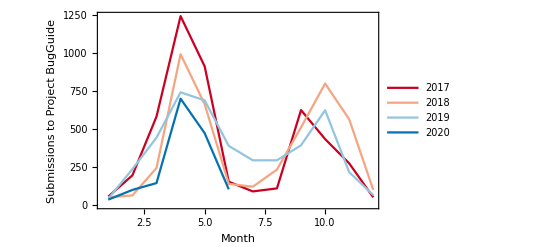

```mathematica
ListLinePlot[Values[bugGuideData],PlotRange->All,Frame->True,FrameLabel->{"Month","Submissions to Project BugGuide"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4]]
```